{{s→InterpolatingFunction[{{0., 100.}}, <>],i→InterpolatingFunction[{{0., 100.}}, <>],r→InterpolatingFunction[{{0., 100.}}, <>]}}

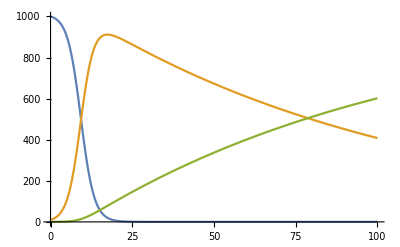

```mathematica
b=0.0005;k=0.01;
system={s'[t]==-b s[t] i[t],i'[t]==b s[t] i[t]-k i[t],r'[t]==k i[t],s[0]==1000,i[0]==10,r[0]==0};
sol=NDSolve[system,{s,i,r},{t,0,100}]
Plot[Evaluate[{s[t],i[t],r[t]}/.sol],{t,0,100}]
```